```mathematica
Quit[]
```

```mathematica
(*  Lewis John Lloyd
	Problem Set 05
	04APR2011
*)
```

0.047311

0.000109567

0.00926356

0.186507

192605.

382.669

21071.7

Piecewise[{{1706.13-3.75×10^7 r^2.-5.20291×10^10 r^4., 0≤r<0.00465}, {-72989.-13751.9 Log[r], 0.00465≤r<0.00473}, {-446.344-202.234 Log[r], 0.00473<r≤0.00535}, {0, True}}]

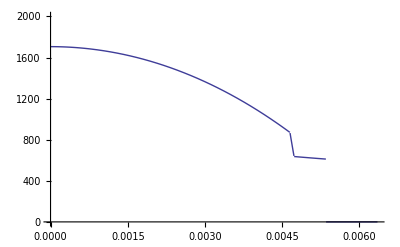

1.0566

1292.6

1706.13

1.31992

681.128

```mathematica
VolumetricHeatSource[r_]=VolumetricHeatSourceNominal(1+0.12(r/RadiusFuel)^2);
Tf[r_]=Limit[Limit[T[r]/.DSolve[1/r D[r kFuel D[T[r],r],r]==-VolumetricHeatSource[r],T[r],r][[1]],C[2]->A0],C[1]->B0];
Tg[r_]=Limit[Limit[T[r]/.DSolve[1/r D[r D[T[r],r],r]==0,T[r],r][[1]],C[2]->A1],C[1]->B1];
Tc[r_]=Limit[Limit[T[r]/.DSolve[1/r D[r D[T[r],r],r]==0,T[r],r][[1]],C[2]->A2],C[1]->B2];
EquationConstants={A0,A1,A2,B0,B1,B2}/.Solve[{Limit[-kFuel r D[Tf[r],r],r->0]==0,
Tf[RadiusFuel]==Tg[RadiusFuel],
Tg[RadiusFuel+ThicknessGap]==Tc[RadiusFuel+ThicknessGap],
Limit[-kFuel r D[Tf[r],r],r->RadiusFuel]==Limit[-kHelium r D[Tg[r],r],r->RadiusFuel],
Limit[-kHelium r D[Tg[r],r],r->(RadiusFuel+ThicknessGap)]==Limit[-kClad r D[Tc[r],r],r->(RadiusFuel+ThicknessGap)],
Limit[-kClad r D[Tc[r],r],r->(RadiusFuel+ThicknessGap+ThicknessClad)]==HeatTransferCoefficientCoolant(Tf[RadiusFuel+ThicknessGap+ThicknessClad]-TemperatureBulk)},{A0,A1,A2,B0,B1,B2}][[1]]//Chop;

(* Fuel Rod Geometry*)
DiameterFuel=0.0093 ;(*[m]*)
RadiusFuel=0.5*DiameterFuel;(*[m]*)
ThicknessClad=0.00062;(*[m]*)
DiameterClad=0.0107;(*[m]*)
ThicknessGap=0.5*(DiameterClad-(DiameterFuel+2*ThicknessClad));(*[m]*)

(* Fuel Rod Material Properties*)
kFuel=2.0;(*[W/m-K]*)
kHelium=0.25;(*[W/m-K]*)
kClad=17.0;(*[W/m-K]*)

(* Core Properties*)
VolumetricHeatSourceNominal=300*10^(6);(*[W/m^3]*)

(* Coolant Properties*)
Pressure=15.5*10^(6);(*[Pa]*)
TemperatureBulk=590;(*[K]*)
VelocityAverage=2.472;(*[m/s]*)

(* Coolant Properties From EES*)
kCoolant=0.5101;(*[W/m-K]*)
SpecificHeatCoolant=5997;(*[J/kg-K]*)
DensityCoolant=688.6;(*[kg/m^3]*)
PrandtlNumberCoolant=0.9625;(*[-]*)
ViscosityCoolant=0.00008187;(*[kg/m-s]*)

(* Flow Channel Geometry*)
Pitch2Diameter=1.32;(*[-]*)

(* Calcuated Values
PerimeterWetted=π*DiameterClad;[m]*)
PerimeterWetted=π*DiameterClad+4*DiameterClad*(Pitch2Diameter-1)(*[m]*)
AreaFlow=DiameterClad^2*(Pitch2Diameter^2-π/4)(*[m^2]*)
DiameterHydraulic=(4AreaFlow)/PerimeterWetted(*[m]*)
MassFlowRate=DensityCoolant AreaFlow VelocityAverage (*[kg/s]*)
ReynoldsNumberCoolant=(DensityCoolant VelocityAverage DiameterHydraulic)/ViscosityCoolant(*[-]*)
NusseltNumberCoolant=0.023 PrandtlNumberCoolant^0.4 ReynoldsNumberCoolant^0.8(*[-]*)
HeatTransferCoefficientCoolant=(NusseltNumberCoolant*kCoolant)/DiameterHydraulic(*[W/m^2-K]*)
Temperature[r_]=Piecewise[{
{Limit[Limit[Tf[r],A0-> EquationConstants[[1]]],B0->EquationConstants[[4]]],0 ≤  r<RadiusFuel},
{Limit[Limit[Tg[r],A1-> EquationConstants[[2]]],B1->EquationConstants[[5]]],RadiusFuel ≤ r< (RadiusFuel+ThicknessGap)},
{Limit[Limit[Tc[r],A2-> EquationConstants[[3]]],B2->EquationConstants[[6]]],(RadiusFuel+ThicknessGap)<r≤ (RadiusFuel+ThicknessGap+ThicknessClad)}
}]
Plot[Temperature[r],{r,0,RadiusFuel+ThicknessGap+ThicknessClad+0.001},PlotRange->{0,2000}]
VolumetricHeat[r_]=Piecewise[{
{VolumetricHeatSource[r],0≤ r≤ RadiusFuel}}];
VolumetricHeatSourceAverage=Integrate[VolumetricHeat[r]r,{r,0,RadiusFuel}]/Integrate[r,{r,0,RadiusFuel}];
VolumetricHeatSourceMaximum=Maximize[{VolumetricHeat[r],0≤ r≤ RadiusFuel},r][[1]];
VolumetricHeatSourceRatio = VolumetricHeatSourceMaximum/VolumetricHeatSourceAverage
TemperatureFuelAverage=Integrate[Temperature[r]r,{r,0,RadiusFuel}]/Integrate[r,{r,0,RadiusFuel}]
TemperatureFuelMaximum = Maximize[{Temperature[r],0≤r≤RadiusFuel},r][[1]]
FuelTemperatureRatio = TemperatureFuelMaximum/TemperatureFuelAverage
TemperatureDifference = TemperatureFuelAverage-Temperature[RadiusFuel+ThicknessGap+ThicknessClad]
```

```mathematica
Quit[]
```

Piecewise[{{1216.67-83333.3 r^2, 0≤r≤0.025}, {(2.60417+1060.42 r)/r, 0.025<r≤0.03}, {0, True}}]

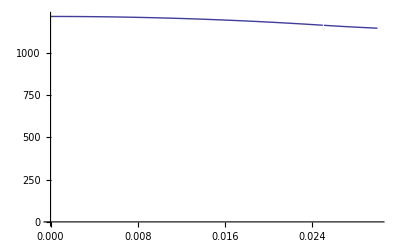

1216.67

1172.54

1147.22

0.0833333

0.0310642

32.1914

374.323

406.549

458.996

520.833

1320.83

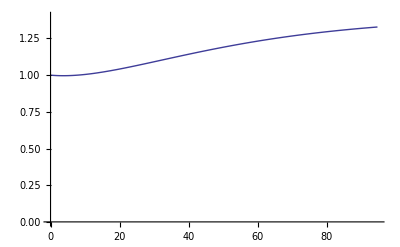

1358.81

558.811

```mathematica
kGraphite=60;(*[W/m-K]*)
SpecificHeatGraphite =710;(* [J/kg-K]*)
DensityGraphite=2267; (*[kg/m^3]*)
DiameterPebble = 0.06; (*[m]*)
DiameterFuel = 0.05; (*[m]*)
RadiusPebble=0.5*DiameterPebble; (*[m]*)
RadiusFuel=0.5*DiameterFuel;(*[m]*)
TemperatureBulk=800;(*[K]*)
HeatTransferCoefficient=500;(*[W/m^2-K]*)
VolumetricHeatSourceInitial=30 10^6;(*[W/m^3]*)
VolumetricHeatSource[t_,r_]=Piecewise[{{
VolumetricHeatSourceInitial(1.5-0.5 ⅇ^(-0.04 t)),0≤ r≤RadiusFuel}}];(*[W/m^3*)
VolumetricHeatSourceFinal=VolumetricHeatSource[∞,0];
TempInner[r_]=Limit[Limit[T[r]/.DSolve[1/r^2 D[r^2 kGraphite D[T[r],r],r]==-VolumetricHeatSourceInitial,T[r],r],C[1]->A0][[1]],C[2]->B0];
TempOuter[r_]=Limit[Limit[T[r]/.DSolve[1/r^2 D[r^2 kGraphite D[T[r],r],r]==0,T[r],r],C[1]->A1][[1]],C[2]->B1];
EquationConstants={A0,A1,B0,B1}/.Solve[{Limit[r^2 TempInner'[r],r->0]==0,
TempInner[RadiusFuel]==TempOuter[RadiusFuel],
-kGraphite TempInner'[RadiusFuel]==-kGraphite TempOuter'[RadiusFuel],
-kGraphite TempOuter'[RadiusPebble]==HeatTransferCoefficient(TempOuter[RadiusPebble]-TemperatureBulk)
},{A0,A1,B0,B1}][[1]]//Expand//Simplify//Chop;
Temperature[r_]=Piecewise[{
{Limit[Limit[TempInner[r],A0->EquationConstants[[1]]],B0->EquationConstants[[3]]],0≤r≤ RadiusFuel},
{Limit[Limit[TempOuter[r],A1->EquationConstants[[2]]],B1->EquationConstants[[4]]],RadiusFuel<r≤RadiusPebble}}]
Plot[Temperature[r],{r,0,RadiusPebble},PlotRange->{0,Temperature[0]}]
TemperatureMaximum=Maximize[{Temperature[r],0≤ r≤RadiusPebble},r][[1]]
TemperatureAverage = Integrate[Temperature[r] r^2,{r,0,RadiusPebble}]/Integrate[r^2,{r,0,RadiusPebble}]
TemperatureSurface=Temperature[RadiusPebble]
VolumePebble = 4/3 π RadiusPebble^3;(*[m^3]*)
VolumeFuel=4/3 π RadiusFuel^3;(*[m^3]*)
SurfacePebble=4π RadiusPebble^2;(*[m^2]*)
CharacteristicRadius=VolumePebble/SurfacePebble;(*[m]*)
BiotPebble =(HeatTransferCoefficient CharacteristicRadius)/kGraphite(*[-]*)
TauPebble = (HeatTransferCoefficient SurfacePebble)/(DensityGraphite SpecificHeatGraphite VolumePebble) (*[1/s]*) 
1/TauPebble
ThetaInitial=TemperatureAverage-TemperatureBulk;
HeatSource[t_]=VolumetricHeatSource[t,0]*VolumeFuel;
Theta[t_]=TempDiff[t]/.DSolve[{D[TempDiff[t],t]==-TauPebble TempDiff[t]+HeatSource[t]/(DensityGraphite SpecificHeatGraphite VolumePebble),
TempDiff[0]==ThetaInitial},TempDiff[t],t][[1]]//FullSimplify;
Theta[0];
Theta[10]
Theta[30]
Theta[60]
ThetaInfinity=Theta[∞]
FinalAverageTemperature=ThetaInfinity+TemperatureBulk
ThetaNormalized[t_]=Theta[t]/Theta[0];
tstar=time/.FindRoot[ThetaNormalized[time]==0.95ThetaNormalized[∞],{time,40}][[1]];
Plot[ThetaNormalized[t],{t,0,tstar},PlotRange->{0,1.4}]
ThetaNormalized[∞];
TempInner[r_]=Limit[Limit[T[r]/.DSolve[1/r^2 D[r^2 kGraphite D[T[r],r],r]==-VolumetricHeatSourceFinal,T[r],r],C[1]->A0][[1]],C[2]->B0];
TempOuter[r_]=Limit[Limit[T[r]/.DSolve[1/r^2 D[r^2 kGraphite D[T[r],r],r]==0,T[r],r],C[1]->A1][[1]],C[2]->B1];
EquationConstants={A0,A1,B0,B1}/.Solve[{Limit[r^2 TempInner'[r],r->0]==0,
TempInner[RadiusFuel]==TempOuter[RadiusFuel],
-kGraphite TempInner'[RadiusFuel]==-kGraphite TempOuter'[RadiusFuel],
-kGraphite TempOuter'[RadiusPebble]==HeatTransferCoefficient(TempOuter[RadiusPebble]-TemperatureBulk)
},{A0,A1,B0,B1}][[1]]//Expand//Simplify//Chop;
Temperature[r_]=Piecewise[{
{Limit[Limit[TempInner[r],A0->EquationConstants[[1]]],B0->EquationConstants[[3]]],0≤r≤ RadiusFuel},
{Limit[Limit[TempOuter[r],A1->EquationConstants[[2]]],B1->EquationConstants[[4]]],RadiusFuel<r≤RadiusPebble}}];
TemperatureMaximum=Maximize[{Temperature[r],0≤ r≤RadiusPebble},r][[1]];
TemperatureAverage = Integrate[Temperature[r] r^2,{r,0,RadiusPebble}]/Integrate[r^2,{r,0,RadiusPebble}]
TemperatureSurface=Temperature[RadiusPebble];
TemperatureAverage-TemperatureBulk

(*Plot[Temperature[r],{r,0,RadiusPebble},PlotRange->{0,Temperature[0]}]*)
```